```mathematica
Φ =Subscript[α, em]/(2 π ω)(1+(1-(2 ω)/(√s))^2)(Log[Ω]-11/6+3/Ω-3/(2 Ω^2)+1/(3 Ω^3));(* Φ = dNγ/dω - photon flux*)
Ω=1+0.71/ω^2 γ^2;
σY= ω Φ Subscript[σ, γh->Vh]; (* σY=(dσ(p+p->p+V+p))/dY - differential rapidity cross section *)
Subscript[σ, γh->Vh]=W^δ;
W=√(2ω √s);
ω=Subscript[M, v]/2 Exp[-Abs[Y]];
γ=(√s)/(2 Subscript[M, p]);
```

```mathematica
constants={s->14000^2,Subscript[M, v]->1,Subscript[M, p]->0.94,Subscript[α, em]->1./137,δ->0.8};
```

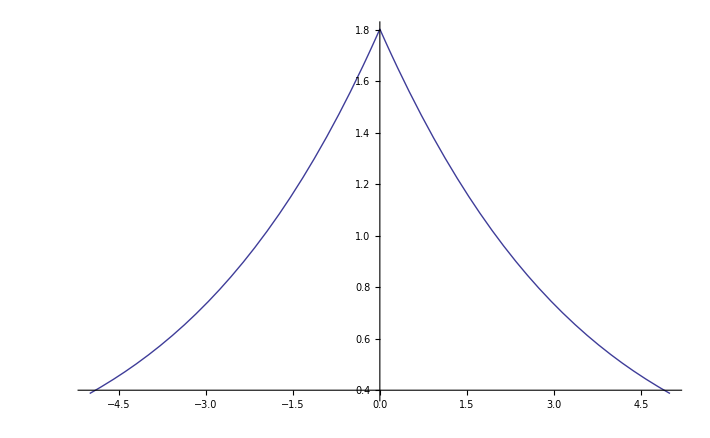

```mathematica
Plot[σY/.constants,{Y,-5,5}]
```